```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mt2,s12,s123,s23,s234,s34,s345,s45,s56};
For[i=1,i<=9,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
RationalReconstruct[a_]:=With[{v=LatticeReduce[{{a,1},{$P,0}}][[1]]},v[[1]]/v[[2]]];
PureIntegralsNEW=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=15;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

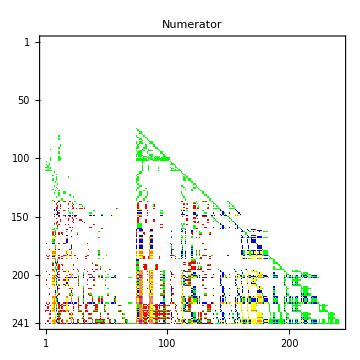
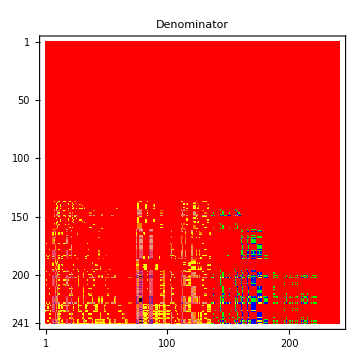
-Graphics- | -Graphics- |

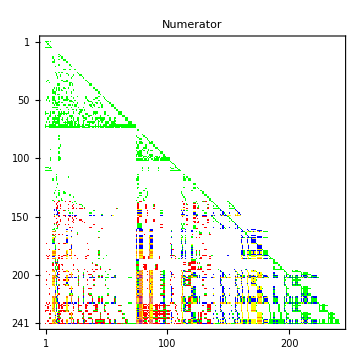
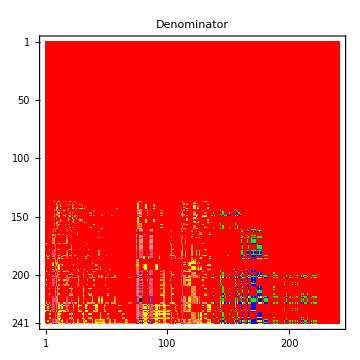
-Graphics- | -Graphics- |

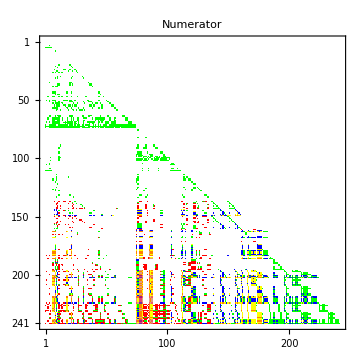
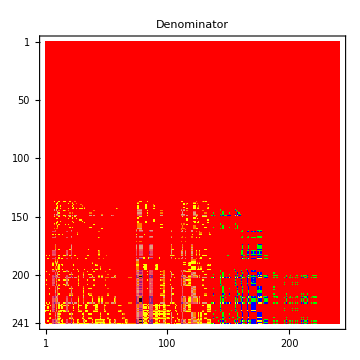
-Graphics- | -Graphics- |

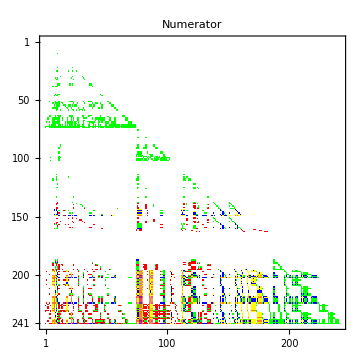
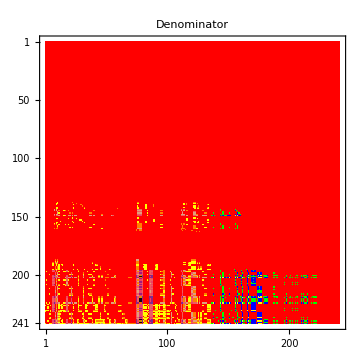
-Graphics- | -Graphics- |

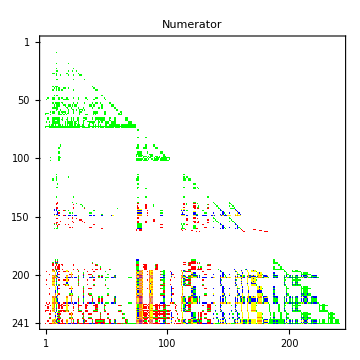
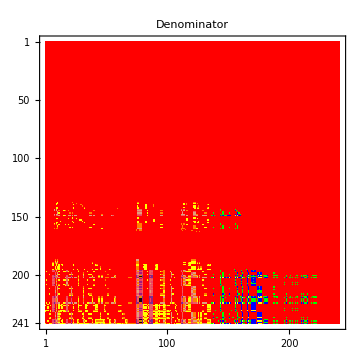
-Graphics- | -Graphics- |

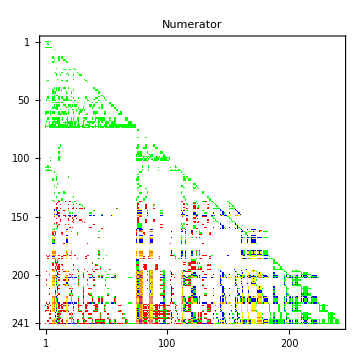
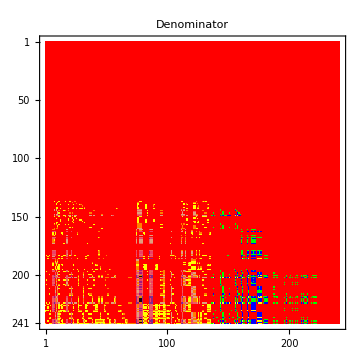
-Graphics- | -Graphics- |

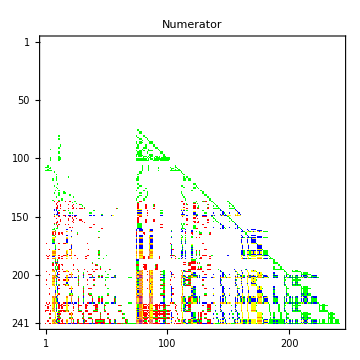
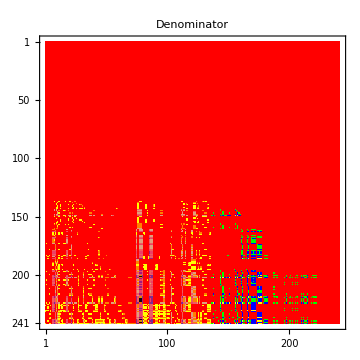
-Graphics- | -Graphics- |

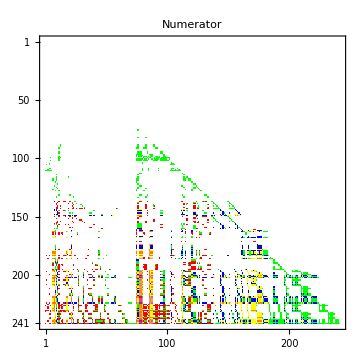
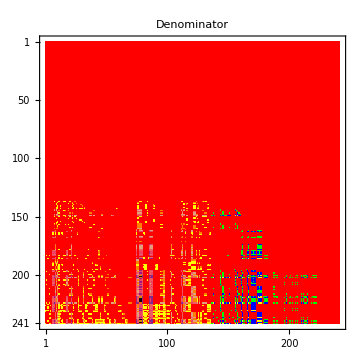
-Graphics- | -Graphics- |

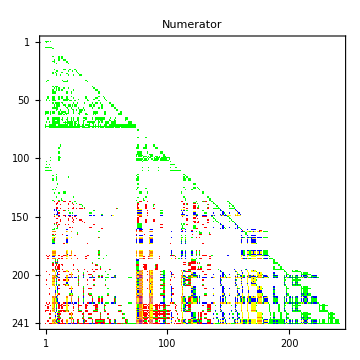
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=241;
For[i=1,i<=9,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Quiet[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P]],{pos,1,Length[dhxbMatrices[s234][[1]]]}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
(*NonZerosPos=ReadList[FileNameJoin[{NotebookDirectory[],"files/NonZeroList.txt"}]];
NumiPowersMat=ConstantArray[-1,241^2];
NumiPowersMat[[NonZerosPos]]=NumiPowers;
DenoPowersMat=ConstantArray[-1,241^2];
DenoPowersMat[[NonZerosPos]]=DenoPowers;*)
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{241,241}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{241,241}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
ArrayReshape[MatReco[s12],{241,241}][[241]]
```

{2080267164/ϵ^3,0,0,931206829/ϵ^3,410447966/ϵ^3,371507461/ϵ^3,(506145827+539149942 ϵ+1749405602 ϵ^2+5062106 ϵ^3+1229339004 ϵ^4)/(58326597 ϵ^4+1497936721 ϵ^5+2139529287 ϵ^6+ϵ^7),(1271799411+1843041821 ϵ+784194816 ϵ^2+926769369 ϵ^3+1110968263 ϵ^4+1452069617 ϵ^5+1315022842 ϵ^6)/(788488150 ϵ^4+1914290017 ϵ^5+1396788416 ϵ^6+1671668021 ϵ^7+720343580 ϵ^8+ϵ^9),(931908396+582137793 ϵ+2078753807 ϵ^2+246600256 ϵ^3+223881183 ϵ^4)/(697060426 ϵ^4+451751223 ϵ^5+1676964967 ϵ^6+ϵ^7),(50256840+505943569 ϵ+423176159 ϵ^2+933424224 ϵ^3)/(2095289326 ϵ^4+728297940 ϵ^5+ϵ^6),(1425831456+174732703 ϵ+586408418 ϵ^2+648673025 ϵ^3+2098352473 ϵ^4)/(297852034 ϵ^4+1749516824 ϵ^5+678267333 ϵ^6+ϵ^7),(1943159457+1381226752 ϵ+800837165 ϵ^2)/(1994422876 ϵ^4+ϵ^5),1391791063/ϵ^3,2080267164/ϵ^3,1812943526/ϵ^3,2080267164/ϵ^3,(1738835267+1450659589 ϵ+860262529 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1836950281+1730357158 ϵ+1804066443 ϵ^2+139806353 ϵ^3+1100299620 ϵ^4)/(58326597 ϵ^4+1497936721 ϵ^5+2139529287 ϵ^6+ϵ^7),(865675197+1655650614 ϵ+2126500384 ϵ^2+171430410 ϵ^3+537208262 ϵ^4)/(58326597 ϵ^4+1497936721 ϵ^5+2139529287 ϵ^6+ϵ^7),(1930942680+1100828557 ϵ+1540662280 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(103406257+148605913 ϵ+1062071112 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(900339041+1956252635 ϵ+194300656 ϵ^2+1848470017 ϵ^3+779810807 ϵ^4+1827323737 ϵ^5)/(697060426 ϵ^5+451751223 ϵ^6+1676964967 ϵ^7+ϵ^8),(1807073739+867660726 ϵ+961384942 ϵ^2)/(1994422876 ϵ^4+ϵ^5),338217191/ϵ^3,(1477638822+1336869347 ϵ+1456285422 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1145000328+348541225 ϵ+1334283523 ϵ^2)/(1994422876 ϵ^4+ϵ^5),2066758514/ϵ^3,(1586283045+1345968210 ϵ)/ϵ^4,1027183816/ϵ^3,460860395/ϵ^3,1861112289/ϵ^3,(583360451+644317420 ϵ+351984088 ϵ^2)/ϵ^5,674939575/ϵ^3,2080267164/ϵ^3,2080267164/ϵ^3,931206829/ϵ^3,(110517211+176747727 ϵ+1624730068 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1359510564+1595452747 ϵ+636300009 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1965338842+347108484 ϵ)/ϵ^4,(349688167+2052135855 ϵ+1281162004 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1599231971+1843468861 ϵ+1982924133 ϵ^2)/(1994422876 ϵ^4+ϵ^5),643532486/ϵ^3,1950463056/ϵ^3,(6267315+1525800358 ϵ)/ϵ^4,(1058388410+2147114600 ϵ)/ϵ^4,1748522635/ϵ^3,(1445787906+1788093895 ϵ+1218963184 ϵ^2)/(1994422876 ϵ^4+ϵ^5),917432149/ϵ^3,1719070594/ϵ^3,(771505517+1967184572 ϵ)/ϵ^4,(2067113514+2081014419 ϵ)/ϵ^4,(993976693+1201842463 ϵ)/ϵ^4,961847692/ϵ^3,1657716495/ϵ^3,(2056704691+1762341237 ϵ+1856634449 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1952073041+1358184148 ϵ+27663382 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1134256894+537796568 ϵ)/ϵ^4,(1520047828+203465766 ϵ+1362387202 ϵ^2)/ϵ^5,(1509122975+1695782623 ϵ)/ϵ^4,1895894849/ϵ^3,183362010/ϵ^3,2080267164/ϵ^3,(205891336+699995307 ϵ)/ϵ^4,1216276818/ϵ^3,(656148990+979445817 ϵ)/ϵ^4,(1509122975+952738713 ϵ)/ϵ^4,1964014747/ϵ^3,(210501815+592859245 ϵ)/ϵ^4,(1774007643+34605788 ϵ)/ϵ^4,(307927411+1949083816 ϵ)/ϵ^4,(1879944166+1737623792 ϵ)/ϵ^4,(225639115+897946788 ϵ)/ϵ^4,(1100188681+94040949 ϵ)/ϵ^4,(957541008+769080959 ϵ)/ϵ^4,(1242230126+842387023 ϵ+37338069 ϵ^2+516546623 ϵ^3+8312521 ϵ^4+2100683996 ϵ^5+521839251 ϵ^6)/(2074949979 ϵ^5+1118055363 ϵ^6+1872399877 ϵ^7+2026924549 ϵ^8+ϵ^9),(95034838+840395256 ϵ+2119380934 ϵ^2+69122749 ϵ^3+1613249506 ϵ^4+1861275112 ϵ^5)/(2071999870 ϵ^4+1879291857 ϵ^5+1669118401 ϵ^6+1559626044 ϵ^7+ϵ^8),(782104187+96993296 ϵ+1254896094 ϵ^2+6120207 ϵ^3+253232840 ϵ^4+942573643 ϵ^5)/(2071999870 ϵ^4+1879291857 ϵ^5+1669118401 ϵ^6+1559626044 ϵ^7+ϵ^8),(1134309081+2013316257 ϵ+1336879608 ϵ^2+219117298 ϵ^3+1017347742 ϵ^4+1356518856 ϵ^5+880133756 ϵ^6+1273099 ϵ^7+1649627417 ϵ^8+1730735398 ϵ^9)/(1276325981 ϵ^5+1969452627 ϵ^6+958663626 ϵ^7+1220899853 ϵ^8+1178593457 ϵ^9+1137269119 ϵ^10+365325123 ϵ^11+ϵ^12),(79038245+518920748 ϵ+1005338878 ϵ^2+1372710053 ϵ^3+398725889 ϵ^4+1510970778 ϵ^5+963748206 ϵ^6+1989140299 ϵ^7+123702105 ϵ^8+196185843 ϵ^9)/(1276325981 ϵ^5+1969452627 ϵ^6+958663626 ϵ^7+1220899853 ϵ^8+1178593457 ϵ^9+1137269119 ϵ^10+365325123 ϵ^11+ϵ^12),(2016959131+2086734851 ϵ+355659842 ϵ^2+1302629303 ϵ^3+976894251 ϵ^4+537543769 ϵ^5+1910615025 ϵ^6)/(2074949979 ϵ^5+1118055363 ϵ^6+1872399877 ϵ^7+2026924549 ϵ^8+ϵ^9),232108975/ϵ^3,686861093/ϵ^3,2039409150/ϵ^3,1421905286/ϵ^3,0,(833117853+227994899 ϵ+219265467 ϵ^2+2097891014 ϵ^3+1614555184 ϵ^4+1643914332 ϵ^5+1179019367 ϵ^6)/(2074949979 ϵ^5+1118055363 ϵ^6+1872399877 ϵ^7+2026924549 ϵ^8+ϵ^9),(1675447015+615742576 ϵ+2068991764 ϵ^2+1007829514 ϵ^3+1641676203 ϵ^4+657516626 ϵ^5)/(2074949979 ϵ^4+1118055363 ϵ^5+1872399877 ϵ^6+2026924549 ϵ^7+ϵ^8),(2016959131+2086734851 ϵ+1978244883 ϵ^2+1171703653 ϵ^3+1857582025 ϵ^4+1198516043 ϵ^5+1546065874 ϵ^6)/(2074949979 ϵ^5+1118055363 ϵ^6+1872399877 ϵ^7+2026924549 ϵ^8+ϵ^9),223862552/ϵ^3,971408753/ϵ^3,1442302856/ϵ^3,506676581/ϵ^3,232108975/ϵ^3,232108975/ϵ^3,(1728256864+2096540386 ϵ+75173033 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(63137771+502564224 ϵ+1360411043 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(439961649+1851662977 ϵ+292820479 ϵ^2)/ϵ^5,(1773403570+449932232 ϵ+1941016864 ϵ^2)/ϵ^5,1725017079/ϵ^3,(1811855340+1332273844 ϵ)/ϵ^4,232108975/ϵ^3,974930775/ϵ^3,0,(1217787709+148453247 ϵ+689049839 ϵ^2+11015569 ϵ^3)/(56302369 ϵ^4+961137085 ϵ^5+ϵ^6),0,128310812/ϵ^3,0,1212408210/ϵ^3,1287238380/ϵ^3,980315902/ϵ^3,1893948010/ϵ^3,(1177072518+1233341998 ϵ+900599749 ϵ^2+380477860 ϵ^3+907699079 ϵ^4+697008443 ϵ^5)/(570507347 ϵ^4+1607401954 ϵ^5+421227076 ϵ^6+1794085404 ϵ^7+ϵ^8),(801023663+2038107034 ϵ+2070882003 ϵ^2+1235080083 ϵ^3+1739320331 ϵ^4+1351756535 ϵ^5+63342678 ϵ^6)/(1212565230 ϵ^5+1732904950 ϵ^6+1953254881 ϵ^7+207748654 ϵ^8+ϵ^9),(1335101249+1165643771 ϵ+1502006703 ϵ^2+1943439974 ϵ^3)/(2095289326 ϵ^4+728297940 ϵ^5+ϵ^6),(2128626310+1915513127 ϵ+1205105679 ϵ^2+904156869 ϵ^3)/(2030830453 ϵ^4+1065787464 ϵ^5+ϵ^6),(626928932+1971022913 ϵ+1509986411 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1082354451+550540947 ϵ+1471840290 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(255262953+35408496 ϵ)/ϵ^4,(360863583+728973800 ϵ)/ϵ^4,(1488130976+150850913 ϵ+1462712310 ϵ^2+357156209 ϵ^3+1116169114 ϵ^4)/(753362795 ϵ^5+603223144 ϵ^6+ϵ^7),(346805565+1195127404 ϵ+352784723 ϵ^2+1235661692 ϵ^3+1764092838 ϵ^4)/(753362795 ϵ^5+603223144 ϵ^6+ϵ^7),(138207549+1983854355 ϵ+718765306 ϵ^2+281843067 ϵ^3)/(1551779579 ϵ^4+1752009157 ϵ^5+ϵ^6),(1225510954+2051499961 ϵ+1692922688 ϵ^2+250974924 ϵ^3)/(1551779579 ϵ^4+1752009157 ϵ^5+ϵ^6),(1050605143+1641650346 ϵ+1979220436 ϵ^2+1913574340 ϵ^3)/(1994422876 ϵ^5+ϵ^6),(1574469395+1906586781 ϵ+1551715279 ϵ^2)/(1994422876 ϵ^4+ϵ^5),525007098/ϵ^3,(1804184678+1940409698 ϵ+1383965788 ϵ^2)/ϵ^5,519555983/ϵ^3,(859301459+1454279723 ϵ+995749145 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(229763991+1942849404 ϵ+960748894 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(1847751342+2009691370 ϵ+1663358369 ϵ^2)/(1994422876 ϵ^4+ϵ^5),(791876341+1165966727 ϵ+1391713748 ϵ^2)/(1994422876 ϵ^4+ϵ^5),592128225/ϵ^3,1532956440/ϵ^3,1763229367/ϵ^3,460356253/ϵ^3,(1202919571+1566782577 ϵ+644691150 ϵ^2)/(1994422876+ϵ),(440106672+1223620488 ϵ+1523455094 ϵ^2+656543694 ϵ^3+1532225344 ϵ^4)/(1994422876 ϵ^2+ϵ^3),(88923623+209386613 ϵ+116500678 ϵ^2+365546855 ϵ^3)/(1994422876 ϵ+ϵ^2),447649018+1252185611 ϵ,1070127065+7229517 ϵ,1616940849+1061085596 ϵ,909637203+328209241 ϵ,(77546985+699133296 ϵ+1597128617 ϵ^2+1607557677 ϵ^3+742421226 ϵ^4)/(2095289326 ϵ+728297940 ϵ^2+ϵ^3),(1728968480+1083711729 ϵ+2092360496 ϵ^2+1271004369 ϵ^3)/(1994422876 ϵ+ϵ^2),(1634596555+827329861 ϵ+1797034981 ϵ^2+43284128 ϵ^3+755297345 ϵ^4)/(1551779579 ϵ+1752009157 ϵ^2+ϵ^3),(1654654413+1023074099 ϵ+1906113737 ϵ^2+333077296 ϵ^3)/(1994422876 ϵ+ϵ^2),(1430296737+460363916 ϵ+1529091249 ϵ^2+837857118 ϵ^3)/(1994422876 ϵ+ϵ^2),(1156369623+1410778151 ϵ+1142899794 ϵ^2)/(1994422876+ϵ),(460600617+706033299 ϵ+1720695631 ϵ^2+787088841 ϵ^3)/(1994422876 ϵ+ϵ^2),(1328596923+1346981019 ϵ+1281100596 ϵ^2+803917884 ϵ^3+2036552221 ϵ^4)/(1994422876 ϵ^2+ϵ^3),(1827448306+1553875987 ϵ+1602564771 ϵ^2+1729583826 ϵ^3)/(1994422876 ϵ+ϵ^2),1741491861+811983572 ϵ,683629637+780224373 ϵ,183441994+1780599659 ϵ,(1649515144+535207164 ϵ+202126231 ϵ^2+1297646399 ϵ^3+1652735216 ϵ^4)/(2095289326 ϵ+728297940 ϵ^2+ϵ^3),(159078217+103293666 ϵ+2034006660 ϵ^2+1908126160 ϵ^3)/(1994422876 ϵ+ϵ^2),(2091136714+2138588861 ϵ+880931374 ϵ^2+177026281 ϵ^3+239448748 ϵ^4)/(1551779579 ϵ+1752009157 ϵ^2+ϵ^3),(880045948+1712203925 ϵ+1782598225 ϵ^2+559220290 ϵ^3)/(1994422876 ϵ+ϵ^2),(2014025187+967891426 ϵ+2077867000 ϵ^2+1306522732 ϵ^3)/(1994422876 ϵ+ϵ^2),(380019608+1274314566 ϵ+800354275 ϵ^2+999294557 ϵ^3)/(349959582 ϵ+ϵ^2),(171851317+461709068 ϵ+93547341 ϵ^2+2047840219 ϵ^3+1971738464 ϵ^4)/(2034878909 ϵ^2+ϵ^3),(1942133653+896488456 ϵ+1175906711 ϵ^2)/ϵ,120777436+1905928775 ϵ,1784465786+726035722 ϵ,(1190207091+1753419329 ϵ+23094949 ϵ^2+478360237 ϵ^3)/(349959582 ϵ+ϵ^2),(1817582333+12594913 ϵ+527332752 ϵ^2+1004727121 ϵ^3+657578188 ϵ^4)/(2034878909 ϵ^2+ϵ^3),(224616872+2083277569 ϵ+1179082535 ϵ^2)/ϵ,(399603757+530513588 ϵ+1607436390 ϵ^2+1757413559 ϵ^3)/(349959582 ϵ+ϵ^2),(959080089+1450462984 ϵ+1841615575 ϵ^2+861745880 ϵ^3)/(349959582 ϵ+ϵ^2),(333189772+1384054070 ϵ+1203760415 ϵ^2+128162949 ϵ^3)/(349959582 ϵ+ϵ^2),(1060385318+1704368939 ϵ+313780308 ϵ^2+429653429 ϵ^3)/(349959582 ϵ+ϵ^2),58917357+1283080804 ϵ,(33332862+1114857734 ϵ+275750041 ϵ^2+723543010 ϵ^3)/(2034878909 ϵ+ϵ^2),(1817582333+1882381738 ϵ+1664163433 ϵ^2+1474987430 ϵ^3+2049688742 ϵ^4)/(2034878909 ϵ^2+ϵ^3),(1163678368+1279358803 ϵ+1918280159 ϵ^2+2005981689 ϵ^3+263380967 ϵ^4)/(2034878909 ϵ^2+ϵ^3),(367360810+135803200 ϵ+170301812 ϵ^2+1216434302 ϵ^3+66478324 ϵ^4)/(2034878909 ϵ^2+ϵ^3),586506608+1072852898 ϵ,(224616872+1264163068 ϵ+150716742 ϵ^2)/ϵ,(224616872+1489338572 ϵ+1843606133 ϵ^2+1443400352 ϵ^3)/ϵ^2,(224616872+1197696693 ϵ+1265566035 ϵ^2+1618564417 ϵ^3)/ϵ^2,(696729888+1762865870 ϵ+1189860915 ϵ^2+1493818550 ϵ^3)/ϵ^2,2100599055+1966812409 ϵ,1035847311 ϵ,687148288 ϵ,602548628 ϵ,(1612436128+1205455078 ϵ+1199062437 ϵ^2)/ϵ,(2083522478+940342015 ϵ+1430623230 ϵ^2)/ϵ,1399203252+917503709 ϵ,(1673380610+1402878774 ϵ+878079840 ϵ^2)/ϵ,132589828 ϵ,1153827067 ϵ,1652007086 ϵ,1847620376 ϵ,1958189982 ϵ,(442693935+35152198 ϵ+306403511 ϵ^2)/ϵ,64782486+496511909 ϵ,(797547533+346881408 ϵ+1418996106 ϵ^2+131520127 ϵ^3)/ϵ^2,1249045876+1681812164 ϵ,(1256894402+531638586 ϵ+351596161 ϵ^2)/ϵ,(19357597+485101439 ϵ+1902135578 ϵ^2)/ϵ,703627424+1407254848 ϵ,(681150399+360620949 ϵ+849123800 ϵ^2)/ϵ,1122340085+1366350826 ϵ,(2076423431+724278990 ϵ+983166531 ϵ^2)/ϵ,33329717+239338294 ϵ,(239622175+333459711 ϵ+1360115466 ϵ^2)/ϵ,1428915676+690387231 ϵ,1059270886+1184781276 ϵ,(1706666833+1728071962 ϵ+2032216345 ϵ^2+1139748562 ϵ^3)/ϵ^2,1791646259+1542147253 ϵ,(1707154071+465821391 ϵ+689778359 ϵ^2+279794326 ϵ^3)/ϵ^2,(2081781862+893517747 ϵ+229344042 ϵ^2)/ϵ,(303130754+888368618 ϵ+1488997871 ϵ^2)/ϵ,(245020452+1301979179 ϵ+795466473 ϵ^2+1312760503 ϵ^3)/ϵ^2,1916063696+817368156 ϵ,1231612233+1252998390 ϵ,(808926510+528857259 ϵ+1546736 ϵ^2)/ϵ,1372278218+207598364 ϵ,(1673380610+1700111484 ϵ+1614828474 ϵ^2)/ϵ,(1673380610+1012939068 ϵ+1349214616 ϵ^2)/ϵ,(224675651+1206012916 ϵ+1806485597 ϵ^2)/ϵ,864936222+1913058068 ϵ,1557651343+1919551270 ϵ,1009573816 ϵ,980021140+1960042280 ϵ,1747185906 ϵ,2110752842 ϵ,629376946+643420924 ϵ,2057475331 ϵ,1560342101+817841550 ϵ,1302194916 ϵ,1328996740+510509833 ϵ,1111926205 ϵ,569255659+927213472 ϵ,1331920806 ϵ,1818372893+2111738100 ϵ,2050558851+1953634055 ϵ,954280352 ϵ,256411750+1302593103 ϵ,382704544+475280187 ϵ}

```mathematica
Position[Diagonal[ArrayReshape[MatReco[s12],{241,241}]],ϵ^2]
```

{{144,2,3,2},{146,2,3,2},{149,2,3,2},{156,2,3,2},{158,2,3,2},{161,2,3,2},{162,2,3,2},{166,2,3,2},{167,2,3,2},{169,2,3,2},{170,2,3,2},{171,2,3,2},{172,2,3,2},{174,2,3,2},{175,2,3,2},{176,2,3,2},{177,2,3,2}}

```mathematica
Expand[ArrayReshape[MatReco[s12],{241,241}][[241,7]]*ϵ^4,Modulus->$P]
```

(506145827+539149942 ϵ+1749405602 ϵ^2+5062106 ϵ^3+1229339004 ϵ^4)/(58326597+1497936721 ϵ+2139529287 ϵ^2+ϵ^3)

```mathematica
Position[ArrayReshape[MatReco[s12],{241,241}][[241]],ϵ^11]
```

{{78,2,1,7,2},{79,2,1,7,2}}

```mathematica
Factor[ArrayReshape[MatReco[s12],{241,241}][[241,78]]*ϵ^4,Modulus->$P]/.n_Integer:>RationalReconstruct[n]
```

(7066 (-1807/10644+ϵ) (8486/20037+ϵ) (-47851/9186-(42758 ϵ)/1183+ϵ^2) (21135/18839+(31258 ϵ)/18627-(48005 ϵ^2)/9288-(22993 ϵ^3)/17052-(6915 ϵ^4)/25984+ϵ^5))/(39889 (-1/2+ϵ) (-1/3+ϵ) ϵ (7471/22526+ϵ) (23601/22183+ϵ) (44063/19631+ϵ) (40681/12052+ϵ) (25526/6179+ϵ))